```mathematica
SDATA={
CI->1.5 10^6,
𝒷->0.380,
𝒹->1.348,
𝒽->0.70 𝒷,
g-> 9.81,
m->779.202996155696,
Jz->12.676,
k-> 5.0 10^6,
b->28000.0,
kpneu-> 50.0 10^6,
bpneu->280000.0,
IF-> 0.3 6 3400/2,
vd-> 2.0,
sd->0.0697710999627824,
ωd-> vd/((𝒹/2-0.0007392599489560887)(1-sd)),
λ->  2,
vmin->0.0001,
ωmin-> vmin/(𝒹/2),
vymin-> -1.0 10^-6
};
```

```mathematica
ξ[t_]={x[t],y[t],θ[t]};
𝕄=DiagonalMatrix[{m,m,Jz}];
𝕧={0,0,0};
𝕘={0,m g,0};
δ=k/(k+kpneu)(𝒹/2-y[t]);
W = π/4  (2 √(δ(𝒹-δ)))𝒷  (kpneu((k+kpneu)/k)δ+bpneu ((k+kpneu)/k) D[δ, t]);
s = 1 - x'[t]/((𝒹/2-δ) θ'[t]);
Bn =Simplify[ (CI 𝒷 𝒹)/W(1+5(δ/𝒽))/(1+3(𝒷 /𝒹))];
GTR = 0.88 (1-Exp[-0.08 Bn])(1-Exp[-9.5s])+0.032;
MRR=0.9/Bn+0.032+(0.5s)/(√Bn);
NTR = GTR - MRR;
TE = NTR/GTR(1-s);
GT = W GTR;
MR = W MRR;
NT = W NTR;
𝕗={
W(GTR Tanh[100 ((𝒹/2-δ)θ'[t]-x'[t])]-MRR Tanh[100 x'[t]] )-IF Tanh[100 x'[t]],
W ,
τ[t]-(𝒹/2-δ) W(GTR Tanh[100 ((𝒹/2-δ)θ'[t]-x'[t])]-MRR Tanh[100 x'[t]] )
};
```

```mathematica
𝕄//MatrixForm
```

(m | 0 | 0
0 | m | 0
0 | 0 | Jz)

```mathematica
𝕧//MatrixForm
```

(0
0
0)

```mathematica
𝕘//MatrixForm
```

(0
g m
0)

```mathematica
EQ=(𝕄. ξ''[t]+𝕧+𝕘-𝕗)/.τ[t]->m(𝒹/2-δ)( 2λ(vd-x'[t])+λ^2(vd t - x[t]));
sol=NDSolve[{EQ⟦1⟧==0,EQ⟦2⟧==0,EQ⟦3⟧==0,θ[0]==0,x[0]==0,y[0]==𝒹/2 -0.00812103,θ'[0]==ωmin,x'[0]==0,y'[0]==vymin}//.SDATA,Join[ξ[t],ξ'[t]],{t,0,100},Method->{"EquationSimplification"->"Residual"}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],y'[t]→InterpolatingFunction[…][t],θ'[t]→InterpolatingFunction[…][t]}}

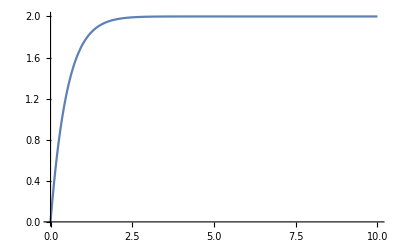

```mathematica
Plot[Evaluate[x'[t]/.sol],{t,0,10},PlotRange->All]
```

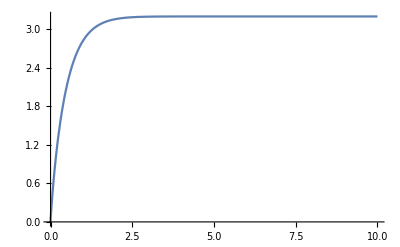

```mathematica
Plot[Evaluate[θ'[t]/.sol],{t,0,10},PlotRange->All]
```

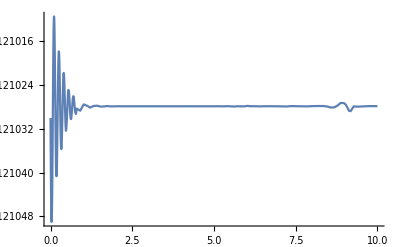

```mathematica
Plot[Evaluate[( y[t]-𝒹/2)//.SDATA/.sol],{t,0,10},PlotRange->All]
```

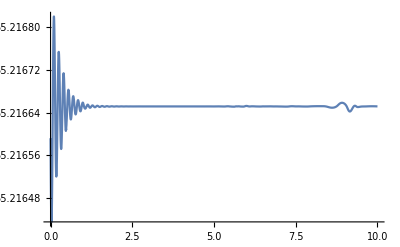

```mathematica
Plot[Evaluate[(Bn)//.SDATA/.sol],{t,0,10},PlotRange->All]
```

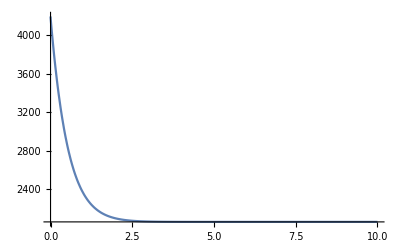

```mathematica
Plot[Evaluate[(m(𝒹/2-δ)( 2λ(vd-x'[t])+λ^2(vd t - x[t])))//.SDATA/.sol],{t,0,10},PlotRange->All]
```

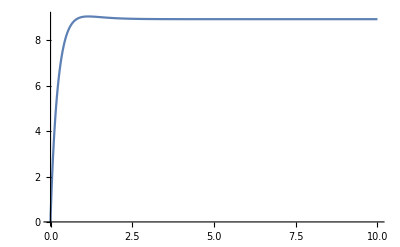

```mathematica
Plot[1/736.499 Evaluate[(θ'[t](m(𝒹/2-δ)( 2λ(vd-x'[t])+λ^2(vd t - x[t]))))//.SDATA/.sol],{t,0,10},PlotRange->All]
```

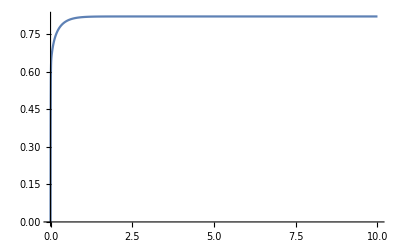

```mathematica
Plot[Evaluate[TE//.SDATA/.sol],{t,0,10},PlotRange->All]
```

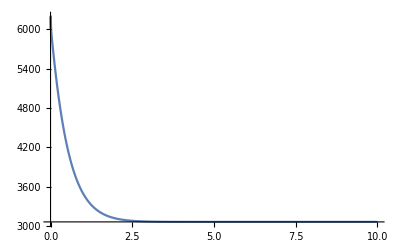

```mathematica
Plot[Evaluate[NT//.SDATA/.sol],{t,0,10},PlotRange->All]
```

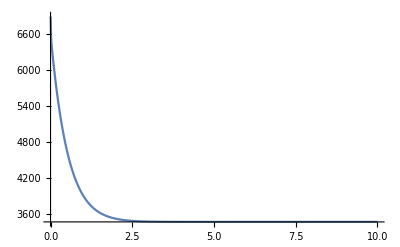

```mathematica
Plot[Evaluate[GT//.SDATA/.sol],{t,0,10},PlotRange->All]
```

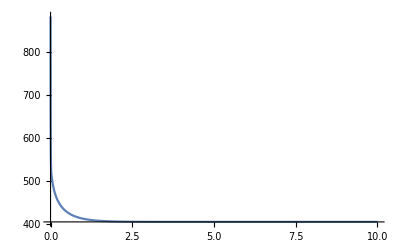

```mathematica
Plot[Evaluate[MR//.SDATA/.sol],{t,0,10},PlotRange->All]
```

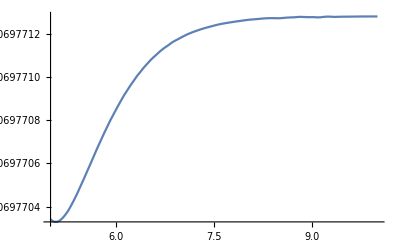

```mathematica
Plot[Evaluate[s//.SDATA/.sol],{t,5,10},PlotRange->All]
```

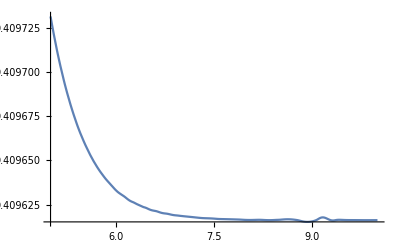

```mathematica
Plot[Evaluate[(GT x'[t])/736.499//.SDATA/.sol],{t,5,10},PlotRange->All]
```

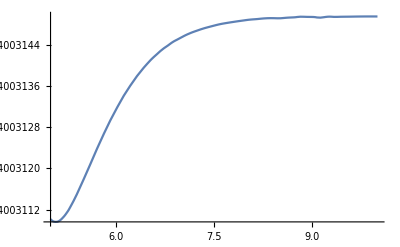

```mathematica
Plot[Evaluate[NTR//.SDATA/.sol],{t,5,10},PlotRange->All]
```